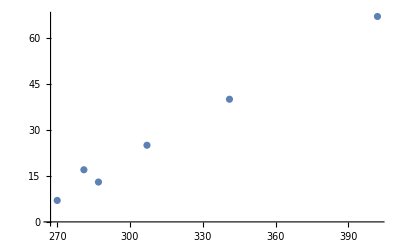

```mathematica
A={{341, 40}, {270, 7}, {281, 17}, {287, 13},{307, 25}, {402, 67}};
ListPlot[A]
```

```mathematica
approx=Fit[A,{1,x},x]
```

-112.032+0.445546 x

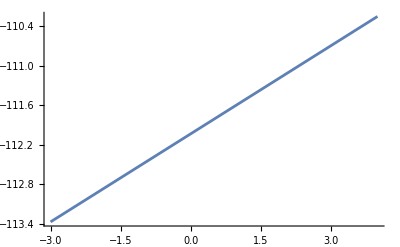

```mathematica
Show[Plot[approx,{x,-3,4}],ListPlot[A,PlotStyle->Red]]
```